```mathematica
PhiHNew[x_,y_]:=(3-(I/8)*Sin[x/4]^2-Sin[x/4]^4 
-(I/8)*Sin[y/4]^8-Sin[y/4]^16
+(I/16)*(Sin[x]Cos[y]^2-2Sin[x]Cos[y] +Sin[x]) )/3
```

```mathematica
Series[PhiHNew[x,y],{x,0,4},{y,0,10}]
```

(1-(ⅈ y^8)/1572864+(ⅈ y^10)/18874368+O[y]^11)+((ⅈ y^4)/192-(ⅈ y^6)/1152+(ⅈ y^8)/15360-(17 ⅈ y^10)/5806080+O[y]^11) x-(ⅈ x^2)/384+(-(ⅈ y^4)/1152+(ⅈ y^6)/6912-(ⅈ y^8)/92160+(17 ⅈ y^10)/34836480+O[y]^11) x^3-(1/768-ⅈ/18432) x^4+O[x]^5

```mathematica
PhiHNew[0,0]
```

1

```mathematica
Series[Log[PhiHNew[x,y]/PhiHNew[0,0]],{x,0,2},{y,0,8}]
```

(-(ⅈ y^8)/1572864+O[y]^9)+((ⅈ y^4)/192-(ⅈ y^6)/1152+(ⅈ y^8)/15360+O[y]^9) x+(-ⅈ/384+(2731 y^8)/201326592+O[y]^9) x^2+O[x]^3

```mathematica
Show[Plot3D[1.000003Abs[PhiHNew[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}],Plot3D[1,{x,-2Pi,2Pi},{y,-2Pi,2Pi}, PlotStyle-> {Black}]]
```

-Graphics3D-

```mathematica
RulePhiNew={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x/4]->(1/(2I))(E^(I*x/4)-E^(-I*x/4)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Cos[y]-> (1/(2))(E^(I*y)+E^(-I*y)),
Sin[y/4]-> (1/(2I))(E^(I*y/4)-E^(-I*y/4))};
```

```mathematica
PhiHNew[x,y]/.RulePhiNew//ExpandAll
```

(26527/32768-(33 ⅈ)/256)+(1/12+ⅈ/24) ⅇ^(-(ⅈ x)/2)+(1/12+ⅈ/24) ⅇ^((ⅈ x)/2)-ⅇ^(-ⅈ x)/192-(7 ⅇ^(ⅈ x))/192-1/96 ⅇ^(-ⅈ x-ⅈ y)+1/96 ⅇ^(ⅈ x-ⅈ y)-1/96 ⅇ^(-ⅈ x+ⅈ y)+1/96 ⅇ^(ⅈ x+ⅈ y)+1/384 ⅇ^(-ⅈ x-2 ⅈ y)-1/384 ⅇ^(ⅈ x-2 ⅈ y)+1/384 ⅇ^(-ⅈ x+2 ⅈ y)-1/384 ⅇ^(ⅈ x+2 ⅈ y)+(715/12288+(7 ⅈ)/192) ⅇ^(-(ⅈ y)/2)+(715/12288+(7 ⅈ)/192) ⅇ^((ⅈ y)/2)-(1001/24576+(7 ⅈ)/384) ⅇ^(-ⅈ y)-(1001/24576+(7 ⅈ)/384) ⅇ^(ⅈ y)+(91/4096+ⅈ/192) ⅇ^(-(3 ⅈ y)/2)+(91/4096+ⅈ/192) ⅇ^((3 ⅈ y)/2)-(455/49152+ⅈ/1536) ⅇ^(-2 ⅈ y)-(455/49152+ⅈ/1536) ⅇ^(2 ⅈ y)+(35 ⅇ^(-(5 ⅈ y)/2))/12288+(35 ⅇ^((5 ⅈ y)/2))/12288-(5 ⅇ^(-3 ⅈ y))/8192-(5 ⅇ^(3 ⅈ y))/8192+ⅇ^(-(7 ⅈ y)/2)/12288+ⅇ^((7 ⅈ y)/2)/12288-ⅇ^(-4 ⅈ y)/196608-ⅇ^(4 ⅈ y)/196608

```mathematica
HNew[i_,j_]:=NIntegrate[Cos[(-i*x/(100^(1/2))-j*y/(100^(1/8))-y^8/1536+y^4*x/192-x^2/24)],{x,-10,10},{y,-10,10}, PrecisionGoal -> 3,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,HNew[i,j]},{i,-7,7,0.1},{j,-7,7,0.1}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew6.csv",data,"CSV"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew1.csv

```mathematica
ListPlot3D[Import["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew1.csv"],ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

```mathematica
PhiHNew1[x_,y_]:=(3-(I)*Sin[x/4]^4-Sin[x/4]^8 
-(I)*Sin[y/3]^6-Sin[y/3]^12
+(I/64)*(Sin[x]^2Sin[y]^3 ) )/3
```

```mathematica
Series[PhiHNew1[x,y],{x,0,5},{y,0,9}]
```

(1-(ⅈ y^6)/2187+(ⅈ y^8)/19683+O[y]^10)+((ⅈ y^3)/192-(ⅈ y^5)/384+(13 ⅈ y^7)/23040-(41 ⅈ y^9)/580608+O[y]^10) x^2+(-ⅈ/768-(ⅈ y^3)/576+(ⅈ y^5)/1152-(13 ⅈ y^7)/69120+(41 ⅈ y^9)/1741824+O[y]^10) x^4+O[x]^6

```mathematica
PhiHNew1[0,0]
```

1

```mathematica
Series[Log[PhiHNew1[x,y]/PhiHNew1[0,0]],{x,0,4},{y,0,8}]
```

(-(ⅈ y^6)/2187+(ⅈ y^8)/19683+O[y]^9)+((ⅈ y^3)/192-(ⅈ y^5)/384+(13 ⅈ y^7)/23040+O[y]^9) x^2+(-ⅈ/768-(ⅈ y^3)/576+(ⅈ y^5)/1152+(761 y^6)/53747712-(13 ⅈ y^7)/69120-(6593 y^8)/483729408+O[y]^9) x^4+O[x]^5

```mathematica
Show[Plot3D[1.0001Abs[PhiHNew1[x,y]],{x,-3Pi,3Pi},{y,-3Pi,3Pi}],Plot3D[1,{x,-3Pi,3Pi},{y,-3Pi,3Pi}, PlotStyle-> {Black}]]
```

-Graphics3D-

```mathematica
RulePhiNew1={Sin[x/4]->(1/(2I))(E^(I*x/4)-E^(-I*x/4)),
Sin[y/6]-> (1/(2I))(E^(I*y/6)-E^(-I*y/6)),
Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Sin[y]->(1/(2I))(E^(I*y)+E^(-I*y))};
```

```mathematica
PhiHNew1[x,y]/.RulePhiNew1//ExpandAll
```

(349/384-ⅈ/8)+(7/96+ⅈ/12) ⅇ^(-(ⅈ x)/2)+(7/96+ⅈ/12) ⅇ^((ⅈ x)/2)-(7/192+ⅈ/48) ⅇ^(-ⅈ x)-(7/192+ⅈ/48) ⅇ^(ⅈ x)+1/96 ⅇ^(-(3 ⅈ x)/2)+1/96 ⅇ^((3 ⅈ x)/2)-1/768 ⅇ^(-2 ⅈ x)-1/768 ⅇ^(2 ⅈ x)+ⅇ^(-2 ⅈ x-ⅈ y)/2048+ⅇ^(2 ⅈ x-ⅈ y)/2048+ⅇ^(-2 ⅈ x+ⅈ y)/2048+ⅇ^(2 ⅈ x+ⅈ y)/2048+ⅇ^(-2 ⅈ x-3 ⅈ y)/6144+ⅇ^(2 ⅈ x-3 ⅈ y)/6144+ⅇ^(-2 ⅈ x+3 ⅈ y)/6144+ⅇ^(2 ⅈ x+3 ⅈ y)/6144-ⅇ^(-ⅈ y)/1024-ⅇ^(ⅈ y)/1024-ⅇ^(-3 ⅈ y)/3072-ⅇ^(3 ⅈ y)/3072-1/3 ⅈ Sin[y/3]^6-1/3 Sin[y/3]^12

```mathematica
HNew2[i_,j_]:=NIntegrate[Cos[(-i*x/(100000000^(1/4))-j*y/(100000000^(1/8))-y^8/768-y^4*x^2/192-x^4/48)],{x,-8,8},{y,-8,8}, PrecisionGoal -> 3,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,HNew2[i,j]},{i,-1000,1000,100},{j,-1000,1000,100}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv",data,"CSV"]
```

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv

```mathematica
ListPlot3D[Import["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv"],ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

```mathematica
MatrixExp[{{0,I*a},{I*a,0}}]
```

{{Cos[a],ⅈ Sin[a]},{ⅈ Sin[a],Cos[a]}}

```mathematica
MatrixExp[{{I*b,0},{0,-I*b}}]
```

{{ⅇ^(ⅈ b),0},{0,ⅇ^(-ⅈ b)}}

```mathematica
P[{{x_},{y_}}]:=x^2+y^4
```

```mathematica
EE={{1/2,0},{0,1/4}}
```

{{1/2,0},{0,1/4}}

```mathematica
MatrixExp[EE]
```

{{√ⅇ,0},{0,ⅇ^(1/4)}}

```mathematica
MatrixExp[EE].{{x},{y}}
```

{{√ⅇ x},{ⅇ^(1/4) y}}

```mathematica
P[MatrixExp[EE].{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
OO={{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
P[OO.MatrixExp[EE].{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
P[MatrixExp[EE].OO.{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
MatrixExp[EE].OO-OO.MatrixExp[EE]
```

{{0,0},{0,0}}

```mathematica
MatrixExp[EE].OO
```

{{√ⅇ,0},{0,-ⅇ^(1/4)}}

```mathematica
Transpose[OO].MatrixExp[EE].OO
```

{{√ⅇ,0},{0,ⅇ^(1/4)}}

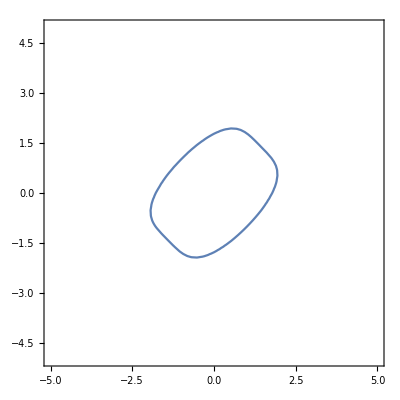

```mathematica
ContourPlot[(1/8)(x+y)^2+(23/384)(x-y)^4==1,{x,-5,5},{y,-5,5}]
```

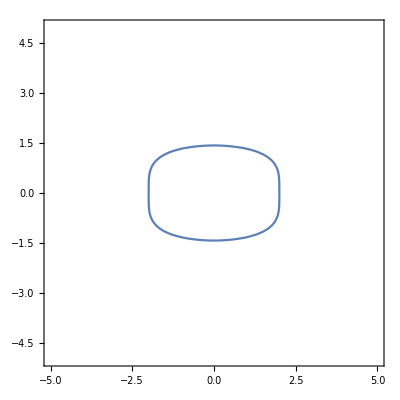

```mathematica
ContourPlot[(1/4)(x)^2+(23/96)(y)^4==1,{x,-5,5},{y,-5,5}]
```